-0.010000500075+2.01259274971818×10^-4343 ⅈ

0.000100015-4.02518549943637×10^-4341 ⅈ

0.0100015-4.02518549943637×10^-4339 ⅈ

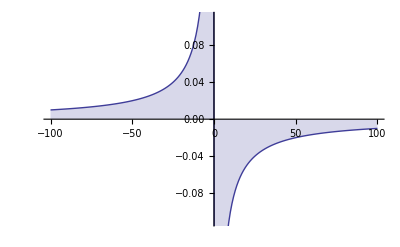

-Graphics-

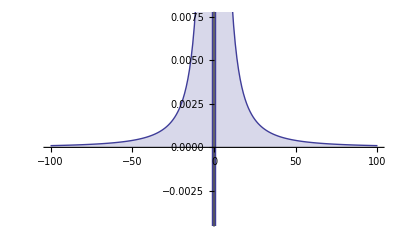

-Graphics-

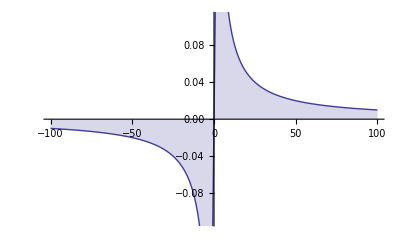

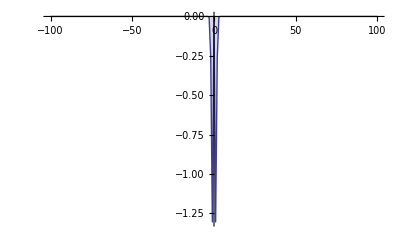

```mathematica
w=2 Pi 3 10^6;
nu=0.05;
kPar=10.5;
Z[x_]:= I Sqrt[Pi] Exp[-x^2] Erfc[-I x];
Zp[x_]:=-2 (1+x Z[x]);
Z[100.0]
Zp[100.0]
100.0 Zp[100.0]
DiscretePlot[Re[Z[eta]],{eta,-100,100,1}]
DiscretePlot[Im[Z[eta]],{eta,-100,100,1}]
DiscretePlot[Re[Zp[eta]],{eta,-100,100,1}]
DiscretePlot[Im[Zp[eta]],{eta,-100,100,1}]
DiscretePlot[Re[eta Zp[eta]],{eta,-100,100,1}]
DiscretePlot[Im[eta Zp[eta]],{eta,-100,100,1}]
```